# Bmad to ICCS Parser

Takes Tao bunch tracking data from the inverse Compton scattering interaction point of any Bmad lattice. Plots x-px phase space for checking against Tao plotting. Converts data to kgm/s for ICCS. Produces momentum ditribution (px,py,pz) in correct form for ICCS.

## Import Bmad Data

```mathematica
(*Load the Bmad data, take off start bumf + end bumf*)
```

```mathematica
rawdata=Drop[Drop[Import["C:/Users/user/Documents/Wolfram Mathematica/Bmad_ICCS_data/0.5%_dat.txt","Words"],21],-1];
```

## Data Parameters

```mathematica
(*data goes x, px, y, py, z, pz etc.*)
(*no. data points*)
ndata = Length[rawdata];
(*no. columns of data*)
ncolumns=13;
(*no. particles*)
npart=ndata/ncolumns;
```

## Phase Space Plot (Validation)

```mathematica
(*Creation of x-px arrays*)
xpxdata=Array[f,{2,npart}];
```

```mathematica
(*un-normalisation and unit conversion*)
Ebeam=150*10^6; (*eV*)
Me=0.511*10^6; (*eV*)
P0=Sqrt[Ebeam^2-Me^2];
eVtoSI=5.36*10^-28; (*kgm/s*)
```

```mathematica
(*Filling arrays*)
For[i=0,i<(npart+1),i++,
(*for x*)
f[1,i]=Interpreter["Number"][ToString[rawdata⟦1+ncolumns*(i-1)⟧]];
(*for px*)
f[2,i]=Interpreter["Number"][ToString[rawdata⟦2+ncolumns*(i-1)⟧]]*(P0*eVtoSI);
];
(*Interpreter + to string convert this to a proper number*)
```

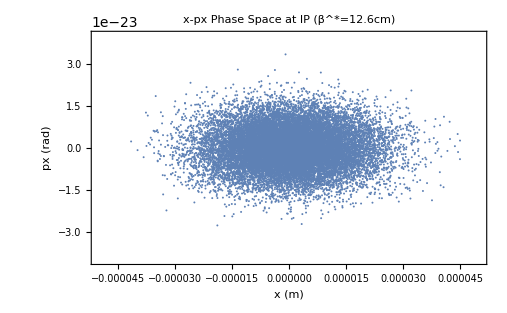

```mathematica
ListPlot[Partition[Riffle[xpxdata⟦1,All⟧,xpxdata⟦2,All⟧],2],PlotRange->{{-50*10^-6,50*10^-6},{-5*10^-4*(P0*eVtoSI),5*10^-4*(P0*eVtoSI)}},Frame->True,AxesLabel->{"x (m)","px (rad)"},PlotLabel->"x-px Phase Space at IP (β^*=12.6cm)"]
```

## Momentum Distribution

```mathematica
(*Creation of momentum array*)
pdata=Array[p,{3,npart}];
```

```mathematica
(*Filling Array*)
For[j=0,j<(npart+1),j++,
(*for px*)
(*pxun=Interpreter["Number"][ToString[rawdata⟦2+ncolumns*(j-1)⟧]]*)
p[1,j]=Interpreter["Number"][ToString[rawdata⟦2+ncolumns*(j-1)⟧]]*(P0*eVtoSI);
(*for py*)
p[2,j]=Interpreter["Number"][ToString[rawdata⟦4+ncolumns*(j-1)⟧]]*(P0*eVtoSI);
(*for pz*)
p[3,j]=(1+Interpreter["Number"][ToString[rawdata⟦6+ncolumns*(j-1)⟧]])*(P0*eVtoSI);
];
```

OverBar[p_x]=p_x/P_0, OverBar[p_y]=p_y/P_0, OverBar[p_z]=(p_z-p_0)/P_0, and also complete the unit conversion.

```mathematica
(*Write new data file*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["C:/Users/user/Documents/Wolfram Mathematica/Bmad_ICCS_data/mom_dat_0.5%.txt",ExportString[Transpose[pdata],"Table"]];
```